# Q5

c==π/4

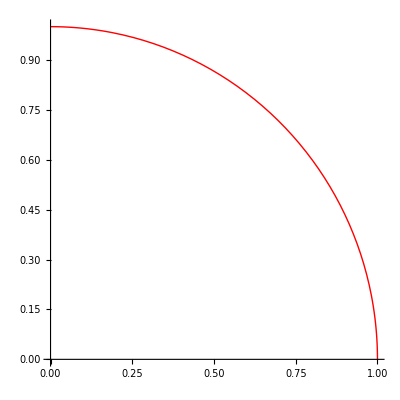

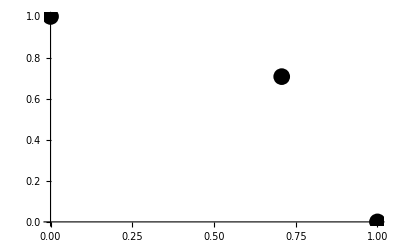

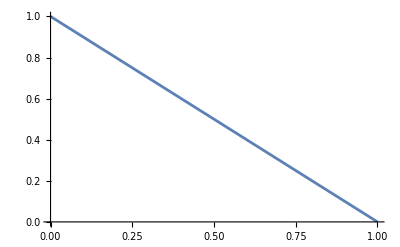

-x/(√(1-x^2))

√2-x

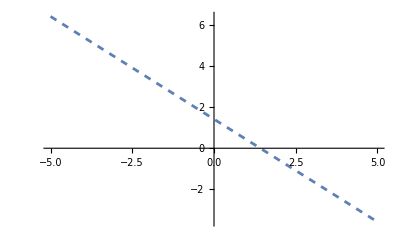

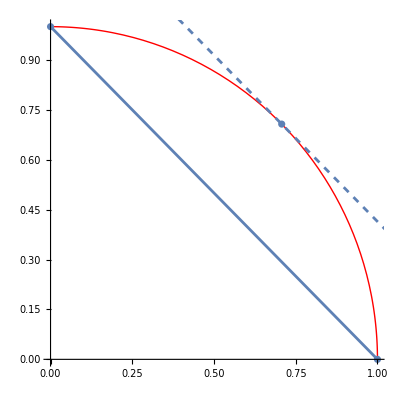

```mathematica
f[x_]:=Sin[x]
g[x_]:=Cos[x]
a=0;
b=Pi/2;
(*i*)
p1 = Reduce[(f[b]-f[a])/(g[b]-g[a])==f'[c]/g'[c]&&a<=c<=b,c]

(*ii*)
f[t_]:=Sin[t];
g[t_]:=Cos[t];
h[t_]:={f[t],g[t]};
g1=ParametricPlot[h[t],{t,a,b},PlotStyle->{Red,Thick}]
(*iii*)
g2=ListPlot[
{
h[a],h[b],h[p1[[2]]]
},
Epilog->{
PointSize[0.03],
Point[
{h[a],h[b],h[p1[[2]]]},
VertexColors->{Purple,Blue,Black}
]
}
]
(*iv*)
g3 = ListPlot[
{
h[a],h[b]
},
Joined->True
]
(*v*)
u[x_]:=Sqrt[1-x^2]
u'[x]
p2 =h[p1[[2]]];
l[x_]=u'[p2[[1]]]*(x-p2[[1]])+p2[[2]]
g4 = Plot[l[x],{x,-5,5},PlotStyle->Dashed]
(*vi*)
Show[g1,g2,g3,g4]
```